## Procesamiento de los datos de piel normal usando mcml con fuente paralela Nr=100, Nz=80,dr=dz=0.005

Datos iniciales y abriendo el fichero

```mathematica
Nr=100;Nz=80;dr=0.005;dz=0.005;
layers={{2.5,250,0.01},{1.7,125,0.25},{1.2,125,2.5}};
zlayer={2,52,83};
SetDirectory["/home/nelia/Documents/Photodynamics/fluence/mcmlcode/paralelo/80x100"];
out=OpenRead["paralelo107.mco"];
```

1000000 Fotones

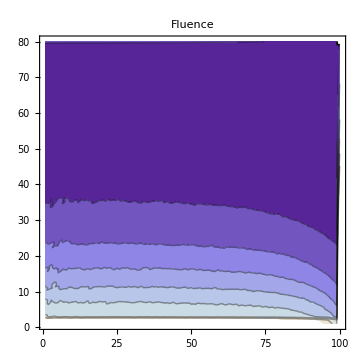
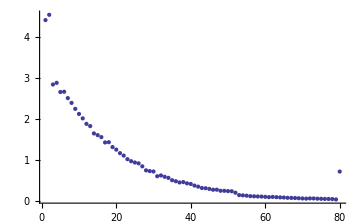

10000000 Fotones

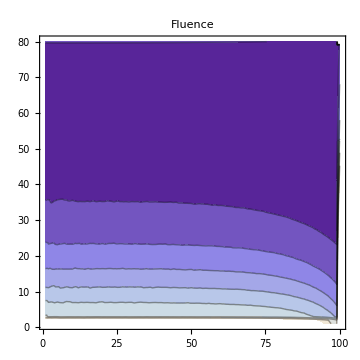
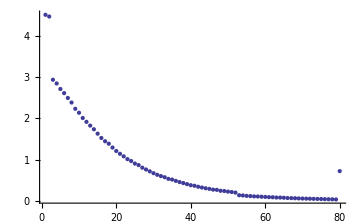

```mathematica
For[i=1,i≤10,i++,
Find[out,"A[nr-1][0]"];
Read[out,Word];
"Numero de photones";
photons=Read[out,Number];
Arz={};
ϕ={};
l=1;
"Leyendo los valores de Arz, guardandolos y normalizando" ;
"Arz/(ΔV N_fotones) ";
For[j=1,j≤ Nr,j++,
AppendTo[Arz,ReadList[out,Number,Nz]/(2 π dr^2 dz(j-0.5) photons )]
];
"Graficos de Arz";
"Calculando la fluencia ϕ=Arz/μa";
k=1;
For[j=1,j<=Nz,j++,
AppendTo[ϕ,Arz[[All,j]]/layers[[k,1]]];
If[i==zlayer[[k]],k++]
];
"Graficos de ϕ";
If[photons==1000000||photons==10000000,
Print[photons," Fotones"];
"Print[ListContourPlot[Arz,ImageSize→Medium],ListPlot[Arz[[1]],ImageSize→Medium]];";
Print[ListContourPlot[ϕ,ImageSize->Medium,PlotLabel->"Fluence"],ListPlot[ϕ[[All,10]],ImageSize->Medium]]
]
]
```

```mathematica
Clear[t,fluence]
```

```mathematica
time=0;Io=10 10^-3 0.2;
fluence=f Io t;
K=Ko;
Soo=4.4 10^-6;
d=8;
S=Table[Soo E^(-d z),{z,0,Nr dr,dr}];


ΓPDT=(βpPDT fluence  O3[t] So[t])/(kpkot+O3[t]);
ecuaciones={D[So[t],t]==-(fluence So[t])/(kpkot+O3[t])βpPDT koskoaA(So[t]+δ) O3[t],
D[O3[t],t]==-ΓPDT-Γmaxmet O3[t]/(k50+O3[t])+K(O3v-O3[t]),
O3[]
}
```

{So'[t]==-(3.78 O3[t] So[t] (16/125+So[t]))/(1/250+O3[t]),O3'[t]==0.037 (2/25-O3[t])-(0.0015 O3[t])/(0.0005+O3[t])-(0.042 O3[t] So[t])/(1/250+O3[t]),O3[0]==1/25}